Symbiosis mediated by sanctions 
Supplement to Yoder and Tiffin, “Sanctions, recognition, and variation in mutualistic symbiosis”

## Terms

This creates a stand-alone model of symbiosis mediated only by host sanctions against non-cooperating symbionts.

Assume infinite populations of interacting, haploid, hosts and symbionts. A host’s ability to sanction a non-cooperative symbiont is determined by its genotype at a single locus; hosts carrying the allele H at this locus are able to sanction, while those carrying the h allele are not. A haploid symbiont is cooperative if it carries the M allele, but not if it carries the m allele. Hosts and symbionts encounter each other at random and initiate symbiosis without respect to their genotypes.

In successful interaction, the host pays a cost C_H of symbiosis and receives a benefit B_H from a cooperative symbiont; the symbionts pay a cost C_S and receive benefit C_S. Hosts interacting with non-mutualist symbionts (m genotype) pay the cost without gaining the benefit. unless they are able to sanction (H genotype). The effectiveness of sanctions, ω, determines how much of the cost of symbiosis a host can avoid when interacting with a non-cooperative symbiont; greater values of ω mean that sanctions do more to reduce the cost of hosting non-cooperators.

## Symbiosis outcomes and fitness

First, a host payoff matrix describes the outcomes of encounters between host genotypes H or h (rows) and symbiont genotypes M and m (columns).

```mathematica
pmH = {{Subscript[B, H]-Subscript[C, H], -(1-ω) Subscript[C, H]},
{ Subscript[B, H]- Subscript[C, H], -Subscript[C, H]}};
MatrixForm[pmH]
```

(B_H-C_H | (-1+ω) C_H
B_H-C_H | -C_H)

Then, a symbiont payoff matrix (same orientation, for convenience).

```mathematica
pmS = {{Subscript[B, S]- Subscript[C, S], (1-ω)  Subscript[B, S]},
{ Subscript[B, S]- Subscript[C, S], Subscript[B, S]}};
MatrixForm[pmS]
```

(B_S-C_S | (1-ω) B_S
B_S-C_S | B_S)

### Fitness expressions

From the payout matrices, we can derive fitness statements for each host and symbiont genotype. For each species, fitness is determined as 1+P, where P is the payout from the symbiosis, determined by the frequencies of the other species’ genotypes.

#### Host fitness

```mathematica
wH=1+Subscript[p, M] pmH[[1,1]]+(1-Subscript[p, M]) pmH[[1,2]];
wh=1+Subscript[p, M] pmH[[2,1]]+(1-Subscript[p, M]) pmH[[2,2]];
wbarH=Subscript[p, H] wH+(1-Subscript[p, H]) wh;
```

Sanctioning hosts have greater fitness than non-sanctioners whenever ωC_H(1-p_M)>0. This requires that C_H>0 (there is a cost to hosting), that ω>0 (sanctions are able to reduce the cost of hosting), and 1-p_M >0 (there are non-cooperative symbionts present in the population).

```mathematica
Simplify[wH-wh]
```

-ω C_H (-1+p_M)

#### Symbiont fitnesses

```mathematica
wM = 1+Subscript[p, H] pmS[[1,1]]+(1-Subscript[p, H]) pmS[[2,1]];
wm = 1+Subscript[p, H] pmS[[1,2]]+(1-Subscript[p, H]) pmS[[2,2]];
wbarM =Subscript[p, M] wM+(1-Subscript[p, M])wm;
```

Non-cooperative symbionts have greater fitness than cooperators whenever C_S/(ωB_S)>ωp_H B_S. This requires that the cost of symbiosis C_S be greater than the benefits of symbiosis B_S weighted by the effectiveness of sanctions ω and the frequency of sanctioning hosts p_H — that is, the probability that a non-cooperator will encounter a sanctioning host, and the degree to which sanctions can prevent non-cooperators from enjoying the benefit of symbiosis.

```mathematica
FullSimplify[wm-wM]
```

C_S-ω B_S p_H

## Allele frequency dynamics

From the above fitness expressions, we can derive per-generation change in the frequency of host and symbiont alleles, following common expressions.

### Host

```mathematica
Subscript[p, H]'=Subscript[p, H] wH/wbarH;
Subscript[Δp, H] =FullSimplify[ Subscript[p, H]'-Subscript[p, H]/.ϵ->1]
```

-(ω C_H (-1+p_H) p_H (-1+p_M))/(-1+C_H (1+ω p_H (-1+p_M))-B_H p_M)

### Symbionts

```mathematica
Subscript[p, M]'=Subscript[p, M] wM/wbarM;
Subscript[Δp, M]=FullSimplify[Subscript[p, M]'-Subscript[p, M]/.ϵ->1]
```

((C_S-ω B_S p_H) (-1+p_M) p_M)/(1+B_S (1+ω p_H (-1+p_M))-C_S p_M)

## Equilibria/stability

We then solve for equilibria in the system (i.e., conditions under which both host and symbiont allele frequencies do not change, Δp_H=Δp_M= 0).

```mathematica
Eqs= Solve[Subscript[Δp, H]==0 && Subscript[Δp, M]==0,{Subscript[p, H],Subscript[p, M]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p_M→1},{p_H→0,p_M→0},{p_H→1,p_M→0}}

None of these are internal equilibria, which demonstrates that selective dynamics modeled with this system of equations do not result in stable maintenance of variation for either the host or symbiont.

To evaluate the stability of these equilibria, we calculate the Jacobean matrix for the system, based on the partial differentiation of each dynamic equation with respect to p_H and p_M.

```mathematica
Jac ={{D[Subscript[Δp, H],Subscript[p, H]],D[Subscript[Δp, M],Subscript[p, H]]},{D[Subscript[Δp, H],Subscript[p, M]],D[Subscript[Δp, M],Subscript[p, M]]}};
```

We then substitute each set of equilibrium conditions into the Jacobean to calculate the eigenvalues at that multivariable equilibrium point.

```mathematica
FullSimplify[Eigenvalues[Jac/.Eqs[[1]]]]
```

{0,(C_S-ω B_S p_H)/(1+B_S-C_S)}

```mathematica
FullSimplify[Eigenvalues[Jac/.Eqs[[2]]]]
```

{-(ω C_H)/(-1+C_H),-C_S/(1+B_S)}

This equilibrium, where p_H=p_M= 0, is only locally stable if C_H>1, which is outside the range we consider. (It would potentially result in nonsensical fitness values.)

```mathematica
FullSimplify[Eigenvalues[Jac/.Eqs[[3]]]]
```

{-(ω C_H)/(1+(-1+ω) C_H),(-ω B_S+C_S)/(-1+(-1+ω) B_S)}

This equilibrium, where p_H=1 and p_M=0, is locally stable when ω B_S<C_S. When  ω B_S>C_S, p_M increases until cooperative symbionts fix.

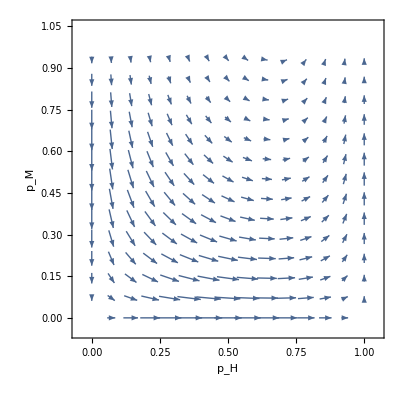

```mathematica
VectorPlot[{Subscript[Δp, H],Subscript[Δp, M]}/.{Subscript[C, H]->0.25,Subscript[B, H]->0.5,Subscript[C, S]->0.25,Subscript[B, S]->0.5,ω->0.75},{Subscript[p, H],0,1},{Subscript[p, M],0,1},FrameLabel->{Subscript[p, H],Subscript[p, M]}]
```